```mathematica
eV = 1;
GeV = 10^9 eV;
keV = 10^3 eV;

mn = 0.939 GeV;
mN = 28 mn;
```

```mathematica
Erecoil[θn_, En_, ω_] :=(2 En mn)/(mn + mN)^2(mn Sin[θn]^2 + mN - Cos[θn]Sqrt[mN^2-mn^2 Sin[θn]^2-(mN(mn + mN)ω)/En])- (mn ω)/(mn + mN)
```

```mathematica
kmax[θn_, En_, ω_] := Min[Sqrt[(ω^2 mN)/(2 Erecoil[θn, En, ω])], Sqrt[2 mN Erecoil[θn, En, ω]]]
```

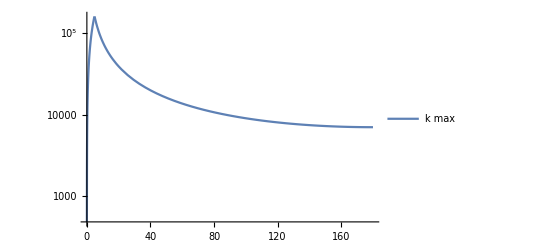

```mathematica
Enpl = 2keV;
ωpl = 1 eV;

LogPlot[{kmax[(π θn)/180, Enpl, ωpl]}, {θn, 0, 180},PlotLegends->{"k max"}]
```